# Lab #8

## Craig Fox

Clear initial definitions

```mathematica
Remove["Global`*"]
```

Differential Equation and Initial and Boundary Conditions

```mathematica
diffEq=(1/v^2)*D[u[x,t],{t,2}]==D[u[x,t],{x,2}]
bc1=u[L/2,t]==0
bc2=u[-L/2,t]==0
ic1=Derivative[0,1][u][x,0]==0
ic2=u[x,0]==(L/2-x)^2*(L/2+x)^2
```

(u^(0,2)[x,t])/v^2==u^(2,0)[x,t]

u[L/2,t]==0

u[-L/2,t]==0

u^(0,1)[x,0]==0

u[x,0]==(L/2-x)^2 (L/2+x)^2

Values for L, v, and tmax

```mathematica
L=2;
v=1;
tmax=L/v;
```

Solving for u

```mathematica
sol=NDSolve[{diffEq,bc1,bc2, ic1, ic2},u,{x,-L/2,L/2},{t,0,tmax}][[1]];
ueq= u/.sol
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 196.562 at t = 2. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[…]

Test plots

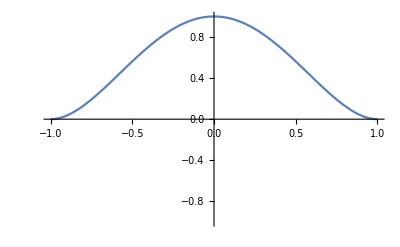

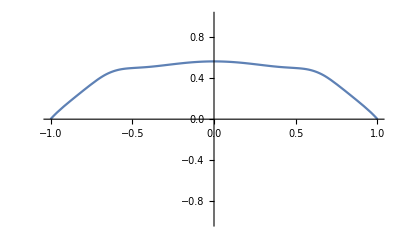

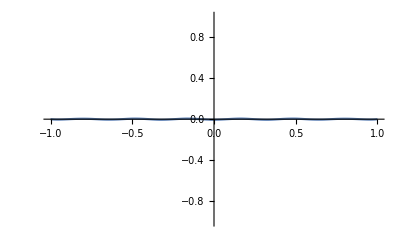

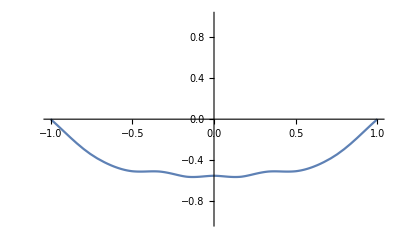

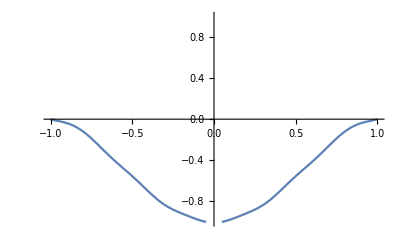

```mathematica
Plot[ueq[x,0],{x,-L/2,L/2},PlotRange->{-1,1}]
Plot[ueq[x,(1/4)*L/v],{x,-L/2,L/2},PlotRange->{-1,1}]
Plot[ueq[x,(1/2)*L/v],{x,-L/2,L/2},PlotRange->{-1,1}]
Plot[ueq[x,(3/4)*L/v],{x,-L/2,L/2},PlotRange->{-1,1}]
Plot[ueq[x,L/v],{x,-L/2,L/2},PlotRange->{-1,1}]
```

Animation

```mathematica
Animate[Plot[ueq[x,t]/.t->time,{x,-L/2,L/2},PlotRange->{-1,1}],
{time,0,tmax},AnimationRunning->False]
```